## Q9001

Import the data from the CSV file

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["radiative_cooling_data.csv","CSV"];
headers=First[data];
Dset=Rest[data];
tData=Dset[[All,1]];
TData=Dset[[All,2]];
Tenv=3.0;
T0=TData[[1]];
```

RK4 Implementation

```mathematica
RK4Solve[k_?NumericQ,tArray_List,y0_?NumericQ,Tenv_?NumericQ]:=Module[{h,n,y,f,k1,k2,k3,k4},h=tArray[[2]]-tArray[[1]];
n=Length[tArray];
y=ConstantArray[0.,n];
y[[1]]=y0;
f[T_]:=-k*(T^4-Tenv^4);
For[i=1,i<n,i++,k1=f[y[[i]]];
k2=f[y[[i]]+h/2*k1];
k3=f[y[[i]]+h/2*k2];
k4=f[y[[i]]+h*k3];
y[[i+1]]=y[[i]]+(h/6)*(k1+2*k2+2*k3+k4);];
y]
```

Objective Function Formulation

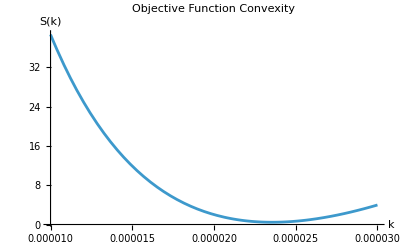

```mathematica
ObjectiveS[k_?NumericQ]:=Module[{yApprox},yApprox=RK4Solve[k,tData,T0,Tenv];
Total[(yApprox-TData)^2]]

Plot[ObjectiveS[k],{k,10^-5,3*10^-5},PlotRange->All,AxesLabel->{"k","S(k)"},PlotLabel->"Objective Function Convexity"]
```

Numerical Optimization (It will take a moment to process. Be patient.)

```mathematica
optResult=FindMinimum[{ObjectiveS[k],10^-5<=k<=3*10^-5},{k,2*10^-5},AccuracyGoal->3];
kStar=k/. optResult[[2]];
Print["Optimal parameter k* = ",kStar]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindMinimum::nrnum: The function value Overflow[] is not a real number at {k} = {-0.00010207}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

Optimal parameter k* = 0.0000238928

Visualizing the Fit

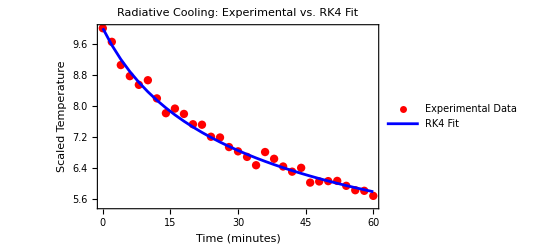

```mathematica
yOpt=RK4Solve[kStar,tData,T0,Tenv];

experimentalPlot=ListPlot[Thread[{tData,TData}],PlotStyle->Directive[Red,PointSize[0.015]],PlotLegends->{"Experimental Data"}];

numericalPlot=ListLinePlot[Thread[{tData,yOpt}],PlotStyle->Blue,PlotLegends->{"RK4 Fit"}];

Show[experimentalPlot,numericalPlot,Frame->True,FrameLabel->{"Time (minutes)","Scaled Temperature"},PlotLabel->"Radiative Cooling: Experimental vs. RK4 Fit"]
```

Extrapolation

```mathematica
ExtrapolateToTarget[kStar_,y0_,Tenv_,targetT_]:=Module[{h,tExtrap,yExtrap,fStar,k1,k2,k3,k4},h=0.5;
tExtrap=0.0;
yExtrap=y0;
fStar[T_]:=-kStar*(T^4-Tenv^4);
While[yExtrap>targetT&&tExtrap<1000,k1=fStar[yExtrap];
k2=fStar[yExtrap+h/2*k1];
k3=fStar[yExtrap+h/2*k2];
k4=fStar[yExtrap+h*k3];
yExtrap=yExtrap+(h/6)*(k1+2*k2+2*k3+k4);
tExtrap+=h;];
tExtrap]

timeToReach5=ExtrapolateToTarget[kStar,T0,Tenv,5.0];
Print["Time to reach T=5: ",timeToReach5," minutes"]
```

Time to reach T=5: 104.5 minutes

```mathematica
NIntegrate[-1/(0.000023892789682710313*(x^4-3^4)),{x,10,5}]
```

104.374

## Q9002

--- Part (c) ---

Estimated slope p (Original AB2): 1.9395

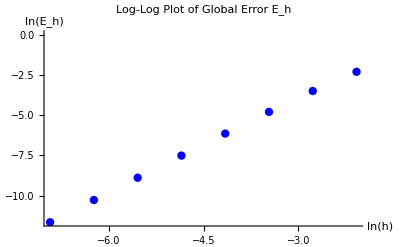

--- Part (e) ---

Estimated new slope p (Extrapolated): 3.00756

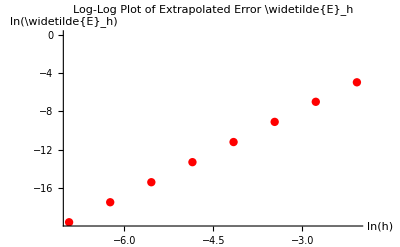

--- Part (f) ---

Estimated Constant |C|: 6.3407

```mathematica
(*Initialize and clear context*)ClearAll["Global`*"];

(*Exact solution evaluated at t=1*)
exactY=E;

(*(b) Compute Y_h for k=3,...,11*)
(*Note:We calculate up to k=11 so we have Y_{h/2} available for k=10 in part (e)*)
Ydata=Table[Module[{h,Nsteps,yVals},h=2^-k;
Nsteps=2^k;
(*Initialize solution array;
indices 1 and 2 correspond to y_0 and y_1*)yVals=ConstantArray[0,Nsteps+1];
yVals[[1]]=1;
yVals[[2]]=Exp[h^2];
(*Two-step Adams-Bashforth Iteration*)For[n=1,n<=Nsteps-1,n++,yVals[[n+2]]=yVals[[n+1]]+h^2 (3 n*yVals[[n+1]]-(n-1)*yVals[[n]]);];
(*Store {h,Y_h}*){h,yVals[[Nsteps+1]]}],{k,3,11}];

(*Extract data specifically for k=3,...,10*)
YhData=Ydata[[1;;8]];

(*Calculate E_h and construct log-log coordinates {log(h),log(E_h)}*)
EhLogData=Map[{Log[#[[1]]],Log[Abs[#[[2]]-exactY]]}&,YhData];

(*(c) Linear Regression for slope p*)
fit1=LinearModelFit[EhLogData,x,x];
slope1=fit1["ParameterTableEntries"][[2,1]];
intercept1=fit1["ParameterTableEntries"][[1,1]];

Print["--- Part (c) ---"];
Print["Estimated slope p (Original AB2): ",slope1];

(*Generate Plot for Original Error*)
plot1=ListPlot[EhLogData,AxesLabel->{"ln(h)","ln(E_h)"},PlotLabel->"Log-Log Plot of Global Error E_h",PlotStyle->{PointSize[0.015],Blue}]

(*(e) Richardson Extrapolation*)
a=4/3;
b=-1/3;

(*Construct\widetilde{Y}_h for k=3,...,10*)
YtildeData=Table[Module[{h,Yh,YhHalf},h=Ydata[[i,1]];
Yh=Ydata[[i,2]];
YhHalf=Ydata[[i+1,2]];(*This is Y_{h/2} since step size halves with k+1*){h,a*YhHalf+b*Yh}],{i,1,8}];

(*Calculate\widetilde{E}_h and construct log-log coordinates*)
EtildeLogData=Map[{Log[#[[1]]],Log[Abs[#[[2]]-exactY]]}&,YtildeData];

(*Linear Regression for extrapolated slope*)
fit2=LinearModelFit[EtildeLogData,x,x];
slope2=fit2["ParameterTableEntries"][[2,1]];

Print["\n--- Part (e) ---"];
Print["Estimated new slope p (Extrapolated): ",slope2];

(*Generate Plot for Extrapolated Error*)
plot2=ListPlot[EtildeLogData,AxesLabel->{"ln(h)","ln(\\widetilde{E}_h)"},PlotLabel->"Log-Log Plot of Extrapolated Error \\widetilde{E}_h",PlotStyle->{PointSize[0.015],Red}]

(*(f) Estimate constant C*)
Cest=Exp[intercept1];

Print["\n--- Part (f) ---"];
Print["Estimated Constant |C|: ",Cest];
```

## Q9003

```mathematica
(*Initialization and Setup*)ClearAll["Global`*"];

A={{10,-9,0,0},{0,10,-9,0},{0,0,10,-9},{-1,-1,-1,10}};
b={1,1,1,1};
P={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}};

Atilde=P.A.Transpose[P];
btilde=P.b;
x0={0,0,0,0};
maxIter=25;
```

```mathematica
(*Iterative Solver Definition Constructs the splitting A=M-N and iterates x_{k+1}=M^{-1}(N x_k+b).*)IterateSystem[mat_,vec_,init_,steps_,method_]:=Module[{D,L,U,M,N,x,resNorms},D=DiagonalMatrix[Diagonal[mat]];
L=LowerTriangularize[mat,-1];
U=UpperTriangularize[mat,1];
If[method=="Jacobi",M=D;N=-(L+U),M=D+L;N=-U];
x=init;
resNorms=ConstantArray[0,steps];
Do[resNorms[[k]]=Norm[vec-mat.x,Infinity];
x=LinearSolve[M,N.x+vec];,{k,1,steps}];
resNorms];
```

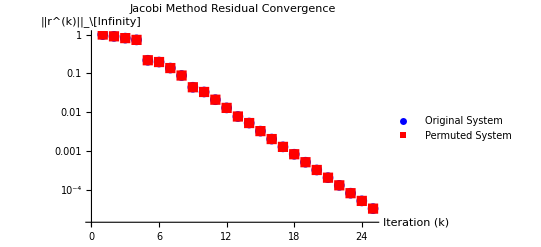

```mathematica
(*---Parts (a)& (b):Jacobi Computations---*)rJ=IterateSystem[A,b,x0,maxIter,"Jacobi"];
rJtilde=IterateSystem[Atilde,btilde,x0,maxIter,"Jacobi"];

plotJ=ListLogPlot[{rJ,rJtilde},PlotStyle->{Blue,Directive[Red,Dashed]},PlotMarkers->Automatic,PlotLabel->"Jacobi Method Residual Convergence",AxesLabel->{"Iteration (k)","||r^(k)||_\\[Infinity]"},PlotLegends->{"Original System","Permuted System"}]
```

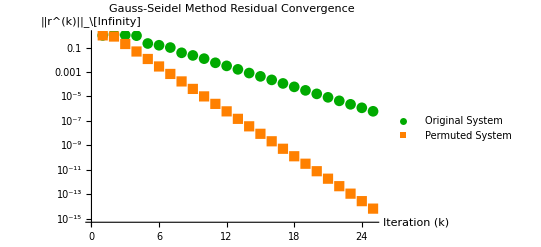

```mathematica
(*---Parts (d)& (e):Gauss-Seidel Computations---*)rGS=IterateSystem[A,b,x0,maxIter,"GS"];
rGStilde=IterateSystem[Atilde,btilde,x0,maxIter,"GS"];

plotGS=ListLogPlot[{rGS,rGStilde},PlotStyle->{Darker[Green],Directive[Orange,Dashed]},PlotMarkers->Automatic,PlotLabel->"Gauss-Seidel Method Residual Convergence",AxesLabel->{"Iteration (k)","||r^(k)||_\\[Infinity]"},PlotLegends->{"Original System","Permuted System"}]
```

```mathematica
(*---Part (f):Spectral Analysis---*)ComputeTGS[mat_]:=Module[{D,L,U},D=DiagonalMatrix[Diagonal[mat]];
L=LowerTriangularize[mat,-1];
U=UpperTriangularize[mat,1];
-Inverse[D+L].U];

Tgs=ComputeTGS[A];
TgsTilde=ComputeTGS[Atilde];

rhoGS=Max[Abs[Eigenvalues[N[Tgs]]]];
rhoGStilde=Max[Abs[Eigenvalues[N[TgsTilde]]]];

Print["Spectral Radius of T_GS (Original): ",rhoGS];
Print["Spectral Radius of T_GS (Permuted): ",rhoGStilde];
```

Spectral Radius of T_GS (Original): 0.518024

Spectral Radius of T_GS (Permuted): 0.2439